```mathematica
minkowski=Plot[{x/3,3x},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->{{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed},{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed}},Ticks->None,PlotRangeClipping->False,AxesLabel->{x,t},Epilog->{GrayLevel[0.4],Text[Style[OverBar[x]],{3.4,1.15}],Text[Style[OverBar[t]],{1.15,3.4}]},ImageSize->Small]
```

-Graphics-

```mathematica
minkowskiTicks=Plot[{x/3,3x},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,Ticks->{{-3,-2,-1,1,2,3},{-3,-2,-1,1,2,3}},PlotStyle->{{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed},{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed}},PlotRangeClipping->False,AxesLabel->{x,t},Epilog->{GrayLevel[0.4],Text[Style[OverBar[x]],{3.4,1.15}],Text[Style[OverBar[t]],{1.15,3.4}]},ImageSize->Small]
```

-Graphics-

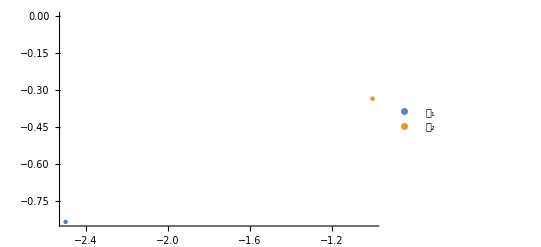

```mathematica
P4a=ListPlot[{{{-2.5,-2.5/3}},{{-1,-1/3}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

```mathematica
lines4a={Graphics[{Thin,Dotted,Line[{{-1,-1/3},{0,-1/3}}]}],Graphics[{Thin,Dotted,Line[{{-2.5,-2.5/3},{0,-2.5/3}}]}]}
```

{-Graphics-,-Graphics-}

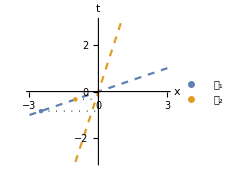

```mathematica
Show[minkowski,lines4a,P4a]
```

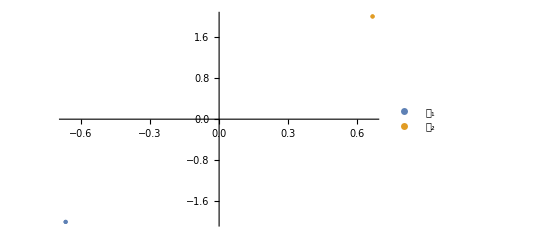

```mathematica
P4b=ListPlot[{{{-2/3,-2}},{{2/3,2}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

```mathematica
lines4b={Graphics[{Thin,Dotted,Line[{{-2/3,-2},{-2/3,0}}]}],Graphics[{Thin,Dotted,Line[{{2/3,2},{2/3,0}}]}]}
```

{-Graphics-,-Graphics-}

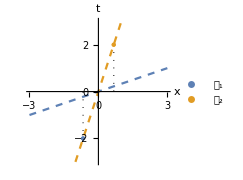

```mathematica
Show[minkowski,lines4b,P4b]
```

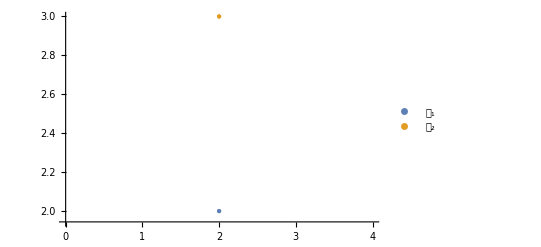

```mathematica
P4c=ListPlot[{{{2,2}},{{2,3}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

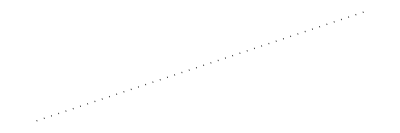
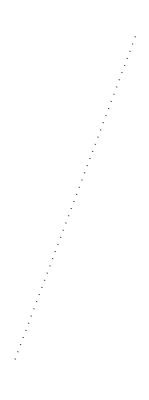
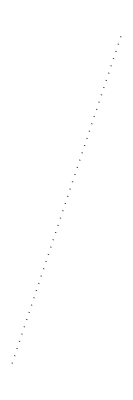
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lines4c={Graphics[{Thin,Dotted,Line[{{2,3},{1,8/3}}]}],Graphics[{Thin,Dotted,Line[{{2,3},{1,1/3}}]}],Graphics[{Thin,Dotted,Line[{{2,2},{1/2,3/2}}]}],Graphics[{Thin,Dotted,Line[{{2,2},{3/2,1/2}}]}]}
```

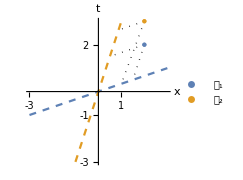

```mathematica
Show[minkowskiTicks,lines4c,P4c]
```